```mathematica
u0[x_]:=Abs[FractionalPart[Abs[x-1/2]]-1/2]
u[x_, k_]:=u0[x*4^k]/4^k
```

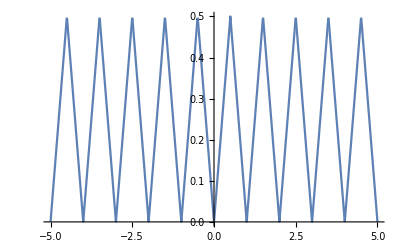

```mathematica
Plot[u[x, 0], {x, -5, 5}]
```

```mathematica
maxK=10
f[x_]:=Sum[u[x, k], {k, 0, maxK}]
p=Plot[f[x], {x, -0.01, 1.01},
MaxRecursion->15,
AspectRatio->1,
PlotStyle->{Black},
PlotRange-> {{-0.02, 1.1}, {-0.01, 0.6}},
AxesLabel->{x,},AxesStyle->Arrowheads[0.05]]
```

10

-Graphics-